```mathematica
par[x_, y_]:=(x y)/(x+ y)
```

```mathematica
par[400000., 10000.]
```

9756.1

```mathematica
Directory[]
```

/home/rui/prc2/simulaciones/sim_2do_cuatri

```mathematica
SetDirectory["/home/rui/prc2/simulaciones/sim_2do_cuatri/pruebas-rui/plots"];
```

```mathematica
s=SemanticImport[ "test.txt"][All, {2->parseComplexLTSpice}];
```

```mathematica
parseComplexLTSpice[sam_]:=StringReplace[sam,StartOfString~~ "("~~mag:Longest[Except["d"]..]~~"dB,"~~phase___~~"°)"~~EndOfString:>{mag, phase}]//First/*Interpreter["Number"]/*ReplaceAll[
{mag_, phase_}:>10^(mag/20) Exp[I Degree phase]
]
```

```mathematica
s=s[All, {2->parseComplexLTSpice}][All, Values];
```

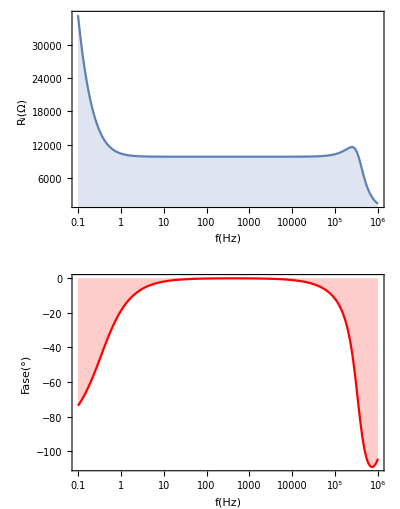

```mathematica
Internal`InheritedBlock[{ListLogLinearPlot},
SetOptions[ListLogLinearPlot, Joined->True,PlotRangePadding->0,Filling->0,PlotRange->Full,PlotTheme->"Detailed",ImagePadding->{{60, All}, {All, All}}];
GraphicsColumn[{
s[ListLogLinearPlot[#, FrameLabel->{"f(Hz)", "R_i(Ω)"}]&, Abs],
s[ListLogLinearPlot[#, PlotRangePadding->{0, 1}, FrameLabel->{"f(Hz)", "Fase("<>ToString[Degree, StandardForm]<>")"},PlotStyle->Red]&, {2->Arg/*(#/Degree&)}]}]
]
```